```mathematica
you:=Select[Flatten[Transpose[{Range[100,999]}].{Range[100,999]}],IntegerDigits[#]==Reverse[IntegerDigits[#]]&]//Max;
AbsoluteTiming@you
```

{1.78617,906609}

```mathematica
optimization:=SelectFirst[#==IntegerReverse@#&]@ReverseSort@Flatten[#ᵀ.#&@{Range[100,999]}]
AbsoluteTiming@optimization
```

{0.0891853,906609}

```mathematica
AbsoluteTiming@SelectFirst[#==IntegerReverse@#&]@ReverseSort@Flatten[#ᵀ.#&@{Range[900,999]}]
```

{0.0239881,906609}

```mathematica
me:=Max@Select[PalindromeQ]@Flatten@Table[i j,{i,100,999},{j,100,999}];
AbsoluteTiming@me
```

{4.10285,906609}

```mathematica
AbsoluteTiming@Max@Select[#==IntegerReverse@#&]@Flatten@Table[i j,{i,100,999},{j,100,999}]
```

{3.89269,906609}

```mathematica
AbsoluteTiming@Max@Select[#==IntegerReverse@#&]@Flatten@ParallelTable[i j,{i,100,999},{j,100,999}]
```

{3.85319,906609}

```mathematica
me1:=SelectFirst[PalindromeQ]@ReverseSort@Flatten@Table[i j,{i,100,999},{j,100,999}];
AbsoluteTiming@me1
```

{0.103928,906609}

```mathematica
AbsoluteTiming@SelectFirst[#==IntegerReverse@#&]@ReverseSort@Flatten@Table[i j,{i,100,999},{j,100,999}]
```

{0.102609,906609}

只快一点点

```mathematica
me2:=Max@SparseArray[{i_,j_}/;PalindromeQ[i j]->i j,{999,999}];
AbsoluteTiming@me2
```

{5.82097,906609}

```mathematica
me3:=SelectFirst[PalindromeQ]@ReverseSort@Flatten@Normal@SparseArray[{i_,j_}->i j,{999,999}];
AbsoluteTiming@me3
```

{3.06607,906609}

```mathematica
Tuples[Range[3],2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
Permutations[Range[3],{2}]
```

{{1,2},{1,3},{2,1},{2,3},{3,1},{3,2}}

```mathematica
Subsets[Range[3],{2}]
```

{{1,2},{1,3},{2,3}}

```mathematica
AbsoluteTiming@SelectFirst[#==IntegerReverse@#&]@ReverseSort@(Times@@@Subsets[Range[100,999],{2}])
```

{0.192735,906609}

```mathematica
AbsoluteTiming@SelectFirst[#==IntegerReverse@#&]@ReverseSort@(Times@@@Tuples[Range[100,999],2])
```

{0.391944,906609}

```mathematica
AbsoluteTiming@SelectFirst[#==IntegerReverse@#&]@ReverseSort@(Times@@@Permutations[Range[100,999],{2}])
```

{0.695188,906609}

```mathematica
999^2
```

998001

```mathematica
906609/993
```

913

```mathematica
ArrayPlot@Table[i j,{i,100,999},{j,100,999}]
```

-Graphics-

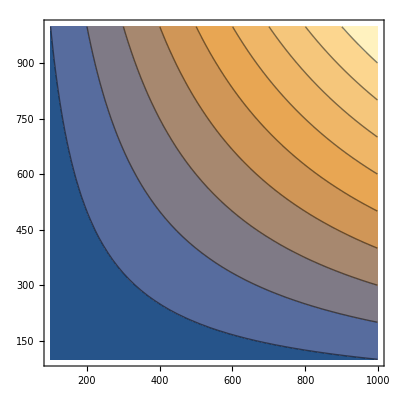

```mathematica
ContourPlot[i j,{i,100,999},{j,100,999}]
```

```mathematica
999 999
998 998 
997 999
```

998001

996004

996003